## Метод срединных квадратов

```mathematica
nMax=100;
sqr[x_]:=Quotient[Mod[x^2,1000000],100];
t[y_]:=RecurrenceTable[{X[n+1]==sqr[X[n]],X[1]==y},
X,
{n,1,nMax}
];
t[143]
```

{143,204,416,1730,9929,5850,2225,9506,3640,2496,2300,2900,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100,4100,8100,6100,2100}

```mathematica
t[131]
```

{131,17,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Графики последовательностей с разными начальным значением

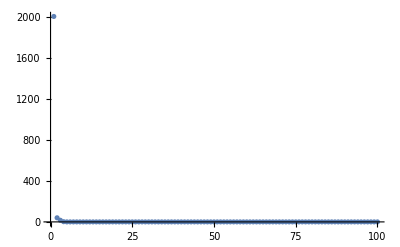
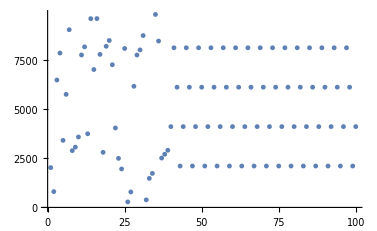
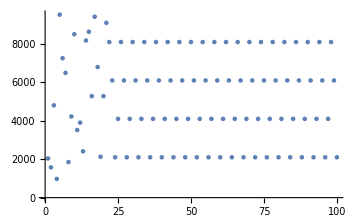
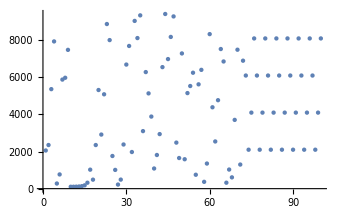
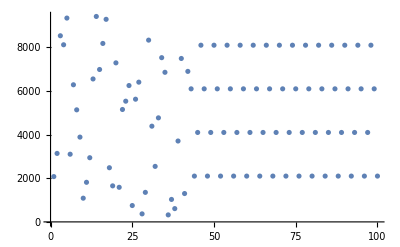
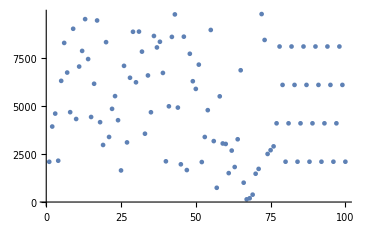
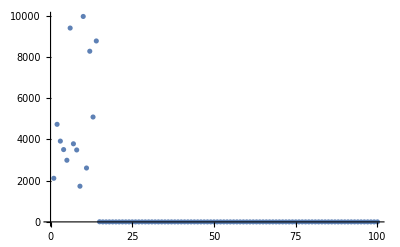
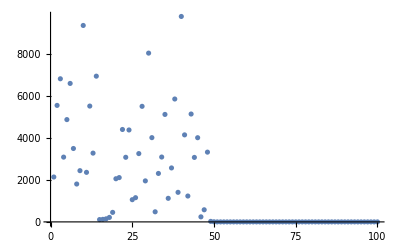
{{-Graphics-,2001},{-Graphics-,2020},{-Graphics-,2039},{-Graphics-,2058},{-Graphics-,2077},{-Graphics-,2096},{-Graphics-,2115},{-Graphics-,2134},{-Graphics-,2153},{-Graphics-,2172},{-Graphics-,2191},{-Graphics-,2210},{-Graphics-,2229},{-Graphics-,2248},{-Graphics-,2267},{-Graphics-,2286},{-Graphics-,2305},{-Graphics-,2324},{-Graphics-,2343},{-Graphics-,2362},{-Graphics-,2381},{-Graphics-,2400},{-Graphics-,2419},{-Graphics-,2438},{-Graphics-,2457},{-Graphics-,2476},{-Graphics-,2495},{-Graphics-,2514},{-Graphics-,2533},{-Graphics-,2552},{-Graphics-,2571},{-Graphics-,2590},{-Graphics-,2609},{-Graphics-,2628},{-Graphics-,2647},{-Graphics-,2666},{-Graphics-,2685},{-Graphics-,2704},{-Graphics-,2723},{-Graphics-,2742},{-Graphics-,2761},{-Graphics-,2780},{-Graphics-,2799},{-Graphics-,2818},{-Graphics-,2837},{-Graphics-,2856},{-Graphics-,2875},{-Graphics-,2894},{-Graphics-,2913},{-Graphics-,2932},{-Graphics-,2951},{-Graphics-,2970},{-Graphics-,2989},{-Graphics-,3008},{-Graphics-,3027},{-Graphics-,3046},{-Graphics-,3065},{-Graphics-,3084},{-Graphics-,3103},{-Graphics-,3122},{-Graphics-,3141},{-Graphics-,3160},{-Graphics-,3179},{-Graphics-,3198},{-Graphics-,3217},{-Graphics-,3236},{-Graphics-,3255},{-Graphics-,3274},{-Graphics-,3293},{-Graphics-,3312},{-Graphics-,3331},{-Graphics-,3350},{-Graphics-,3369},{-Graphics-,3388},{-Graphics-,3407},{-Graphics-,3426},{-Graphics-,3445},{-Graphics-,3464},{-Graphics-,3483},{-Graphics-,3502},{-Graphics-,3521},{-Graphics-,3540},{-Graphics-,3559},{-Graphics-,3578},{-Graphics-,3597},{-Graphics-,3616},{-Graphics-,3635},{-Graphics-,3654},{-Graphics-,3673},{-Graphics-,3692},{-Graphics-,3711},{-Graphics-,3730},{-Graphics-,3749},{-Graphics-,3768},{-Graphics-,3787},{-Graphics-,3806},{-Graphics-,3825},{-Graphics-,3844},{-Graphics-,3863},{-Graphics-,3882},{-Graphics-,3901},{-Graphics-,3920},{-Graphics-,3939},{-Graphics-,3958},{-Graphics-,3977},{-Graphics-,3996}}

```mathematica
Table[
{ListPlot[t[s]],s},
{s,2001,4001,19}
]
```